```mathematica
(*** to calculate the unit of rapidity ***)
```

```mathematica
sqrtNN=5020
```

5020

```mathematica
Ebeam=0.5*sqrtNN
Mbeam=0.938
Pbeam=√(Ebeam^2-Mbeam^2)
ybeam=0.5*Log[(Ebeam+Pbeam)/(Ebeam-Pbeam)]
```

2510.

0.938

2510.

8.58519

```mathematica
sigma=1.9
eta0=2.0
```

1.9

2.

```mathematica
sigma=2.5
eta0=1.4
```

2.5

1.4

```mathematica
f1[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1+eta/ybeam)UnitStep[ybeam+eta]
```

```mathematica
f2[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1-eta/ybeam)*UnitStep[ybeam-eta]
```

```mathematica
f3[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*UnitStep[ybeam-eta]
```

```mathematica
MaxValue[f1[eta],eta]
1+eta0/ybeam
MaxValue[f1[eta],eta]/(1+eta0/ybeam)
MaxValue[f1[eta],eta]/(1+eta0/ybeam)^3
```

1.51346

1.16307

1.30126

0.961948

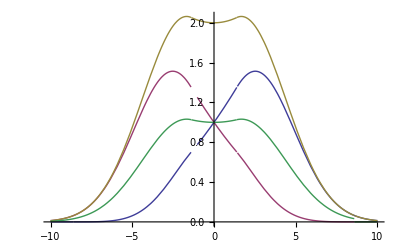

```mathematica
Plot[{f1[eta],f2[eta],f1[eta]+f2[eta],f3[eta]},{eta,-10,10}]
```

```mathematica
f1[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1+eta/ybeam)^2 UnitStep[ybeam+eta]
```

```mathematica
f2[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1-eta/ybeam)^2*UnitStep[ybeam-eta]
```

```mathematica
f3[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1+(eta/ybeam)^2)*UnitStep[ybeam-eta]
```

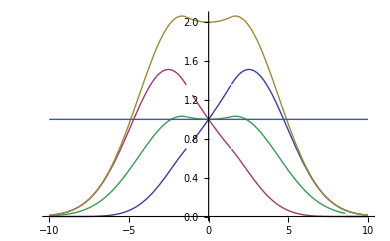

```mathematica
Plot[{f1[eta],f2[eta],f1[eta]+f2[eta],f3[eta],1},{eta,-10,10}]
```

```mathematica
(*** right-moving direction ***)
```

```mathematica
MaxValue[f1[eta],eta]
1+eta0/ybeam
MaxValue[f1[eta],eta]/(1+eta0/ybeam)^2
MaxValue[f1[eta],eta]/(1+eta0/ybeam)^3
```

1.51346

1.16307

1.11881

0.961948

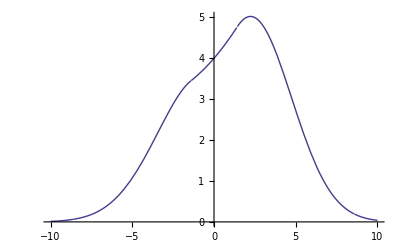

```mathematica
Plot[3f1[eta]+f2[eta],{eta,-10,10}]
```

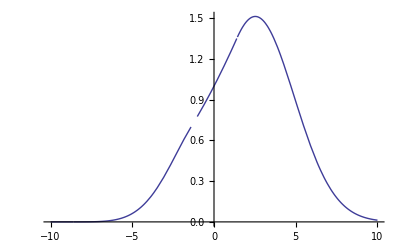

```mathematica
Plot[f1[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f1[eta],{eta,-10,10}]
```

10.255

```mathematica
NIntegrate[f1[eta],{eta,-0.5,0.5}]
```

1.00113

```mathematica
NIntegrate[f1[eta],{eta,-1,1}]
```

2.00905

```mathematica
NIntegrate[f1[eta],{eta,-2,2}]
```

4.06041

```mathematica
NIntegrate[f1[eta],{eta,-3,3}]
```

6.01954

```mathematica
(*** left-moving direction ***)
```

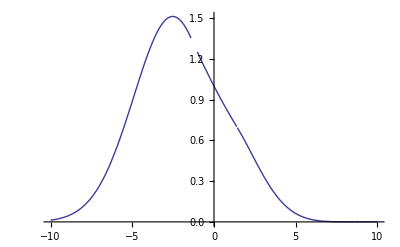

```mathematica
Plot[f2[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f2[eta],{eta,-10,10}]
```

10.255

```mathematica
NIntegrate[f2[eta],{eta,-0.5,0.5}]
```

1.00113

```mathematica
NIntegrate[f2[eta],{eta,-1,1}]
```

2.00905

```mathematica
NIntegrate[f2[eta],{eta,-2,2}]
```

4.06041

```mathematica
NIntegrate[f2[eta],{eta,-3,3}]
```

6.01954

```mathematica
(*** left & right moving ***)
```

```mathematica
f3[eta_]:=Exp[-(Abs[eta]-eta0)^2/(2 sigma^2)UnitStep[Abs[eta]-eta0]]*(1+(eta/ybeam)^2)*UnitStep[ybeam-eta]
```

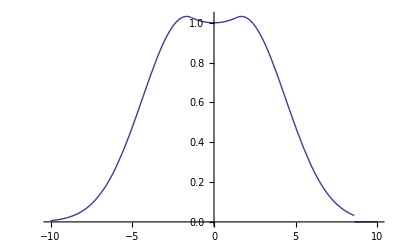

```mathematica
Plot[f3[eta],{eta,-10,10}]
```

```mathematica
NIntegrate[f3[eta],{eta,-10,10}]
```

10.2319

```mathematica
NIntegrate[f3[eta],{eta,-0.5,0.5}]
```

1.00113

```mathematica
NIntegrate[f3[eta],{eta,-1,1}]
```

2.00905

```mathematica
NIntegrate[f3[eta],{eta,-2,2}]
```

4.06041

```mathematica
NIntegrate[f3[eta],{eta,-3,3}]
```

6.01954